```mathematica
x^3-x
```

-x+x^3

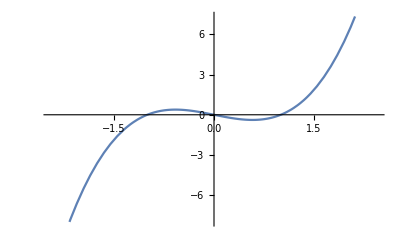

```mathematica
Plot[-x+x^3,{x,-2.449489742783178,2.449489742783178}]
```

```mathematica
FullSimplify[Normalize@{x,-x+x^3}.Normalize@{x,α},{x,α}∈Reals]
```

((x+(-1+x^2) α) Sign[x])/(√((2-2 x^2+x^4) (x^2+α^2)))

```mathematica
Manipulate[Plot[((x+(-1+x^2) α) Sign[x])/(√((2-2 x^2+x^4) (x^2+α^2))),{x,-1.3153266657381688,1.3153266657381688}],{α,-1.5531229146464538,1.5531229146464538}]
```

```mathematica
D[((x+(-1+x^2) 0) Sign[x])/(√((2-2 x^2+x^4) (x^2+0^2))),x]==0
```

Sign[x]/(√(x^2 (2-2 x^2+x^4)))-(x (x^2 (-4 x+4 x^3)+2 x (2-2 x^2+x^4)) Sign[x])/(2 (x^2 (2-2 x^2+x^4))^(3/2))+(x Sign'[x])/(√(x^2 (2-2 x^2+x^4)))==0

```mathematica
Sign[x]/(√(x^2 (2-2 x^2+x^4)))-(x (x^2 (-4 x+4 x^3)+2 x (2-2 x^2+x^4)) Sign[x])/(2 (x^2 (2-2 x^2+x^4))^(3/2))+(x Sign'[x])/(√(x^2 (2-2 x^2+x^4)))
```

Sign[x]/(√(x^2 (2-2 x^2+x^4)))-(x (x^2 (-4 x+4 x^3)+2 x (2-2 x^2+x^4)) Sign[x])/(2 (x^2 (2-2 x^2+x^4))^(3/2))+(x Sign'[x])/(√(x^2 (2-2 x^2+x^4)))

```mathematica
FullSimplify[Sign[x]/(√(x^2 (2-2 x^2+x^4)))-(x (x^2 (-4 x+4 x^3)+2 x (2-2 x^2+x^4)) Sign[x])/(2 (x^2 (2-2 x^2+x^4))^(3/2))+(x Sign'[x])/(√(x^2 (2-2 x^2+x^4)))]
```

(x^3 (-2 x (-1+x^2) Sign[x]+(2-2 x^2+x^4) Sign'[x]))/((x^2 (2-2 x^2+x^4))^(3/2))

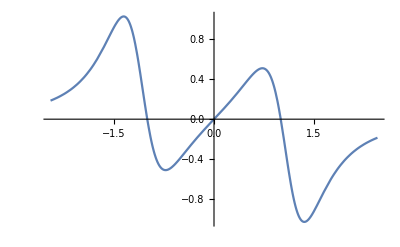

```mathematica
Plot[(x^3 (-2 x (-1+x^2) Sign[x]+(2-2 x^2+x^4) 0))/((x^2 (2-2 x^2+x^4))^(3/2)),{x,-2.449489742783178,2.449489742783178}]
```

```mathematica
FullSimplify[Normalize@{x,-(2 x^4 (-1+x^2) Sign[x])/((x^2 (2-2 x^2+x^4))^(3/2))}.Normalize@{x,0},x∈Reals]
```

1/(√(1+(4 (-1+x^2)^2 Sign[x]^2)/((2-2 x^2+x^4)^3)))

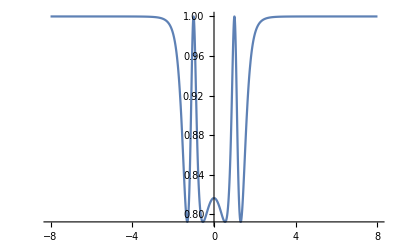

```mathematica
Plot[1/(√(1+(4 (-1+x^2)^2 Sign[x]^2)/((2-2 x^2+x^4)^3))),{x,-8,8}]
```

```mathematica
(x^3 (-2 x (-1+x^2) Sign[x]+(2-2 x^2+x^4) 0))/((x^2 (2-2 x^2+x^4))^(3/2))
```

-(2 x^4 (-1+x^2) Sign[x])/((x^2 (2-2 x^2+x^4))^(3/2))

```mathematica
ComplexPlot[z^2,{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
ComplexPlot[z,{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
ComplexPlot[Exp[z],{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
-1/f'[x]
```

-1/f'[x]

```mathematica
x^5-x^4+x^3-x^2+x-1
```

-1+x-x^2+x^3-x^4+x^5

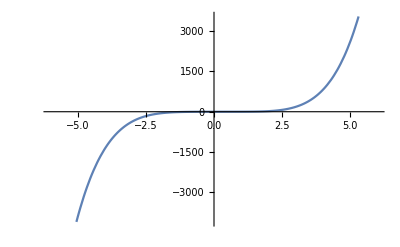

```mathematica
Plot[-1+x-x^2+x^3-x^4+x^5,{x,-6.,6.}]
```

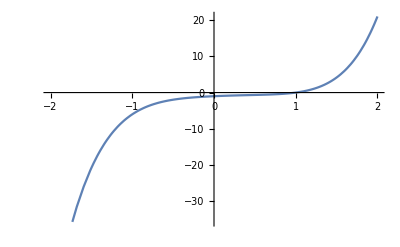

```mathematica
Plot[-1+x-x^2+x^3-x^4+x^5,{x,-2,2}]
```

```mathematica
ContourPlot3D[y^2==x^3+2x+1,{x,-2,2},{y,-2,2}]
```

ContourPlot3D::argrx: ContourPlot3D called with 3 arguments; 4 arguments are expected.

ContourPlot3D[y^2==x^3+2 x+1,{x,-2,2},{y,-2,2}]

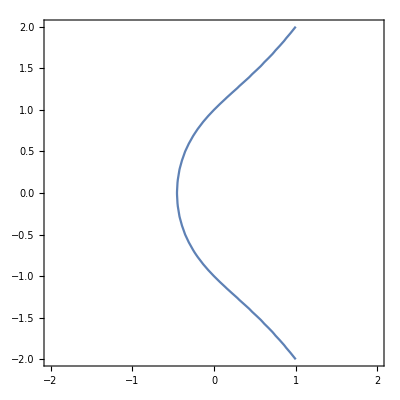

```mathematica
ContourPlot[y^2==x^3+2x+1,{x,-2,2},{y,-2,2}]
```

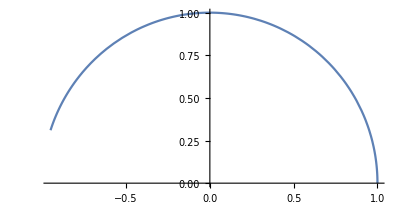

```mathematica
ParametricPlot[
{(1-t^2)/(1+t^2),(2t)/(1+t^2)}
,{t,0,2π}]
```

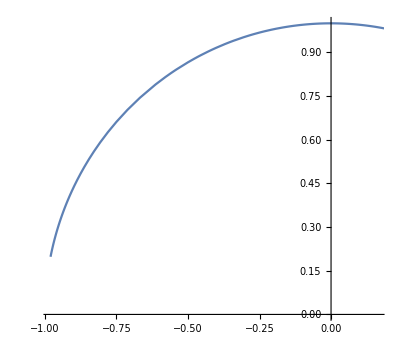

```mathematica
ParametricPlot[
{(1-t^2)/(1+t^2),(2t)/(1+t^2)}
,{t,0,10}]
```

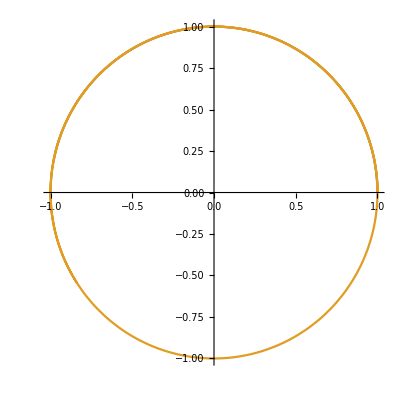

```mathematica
ParametricPlot[{
{(1-t^2)/(1+t^2),(2t)/(1+t^2)},
{Cos[t],Sin[t]}
},{t,0,10}]
```

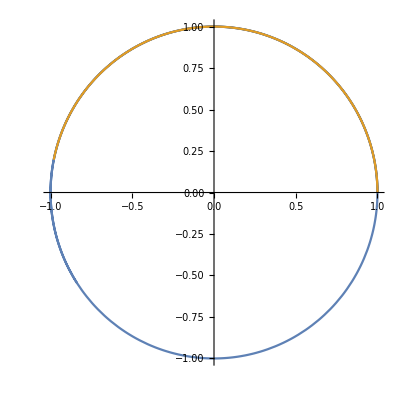

```mathematica
ParametricPlot[{
{Cos[t],Sin[t]},
{(1-t^2)/(1+t^2),(2t)/(1+t^2)}
},{t,0,10}]
```

```mathematica
ParametricPlot[{
{Cos[t],Sin[t]},
{(1-t^2)/(1+t^2),(2t)/(1+t^2)}
},{t,0,10}]
```

-Graphics-

```mathematica
Manipulate[
ContourPlot[y^2==a x^3+b x+1,{x,-2,2},{y,-2,2}]
,{a,-2,2},{b,-2,2}]
```

```mathematica
Solve[y==x^3+x^2+x,x]
```

{{x→-1/3+(2 2^(1/3))/(3 (-7-27 y+3 √3 √(3+14 y+27 y^2))^(1/3))-((-7-27 y+3 √3 √(3+14 y+27 y^2))^(1/3))/(3 2^(1/3))},{x→-1/3-(2^(1/3) (1+ⅈ √3))/(3 (-7-27 y+3 √3 √(3+14 y+27 y^2))^(1/3))+((1-ⅈ √3) (-7-27 y+3 √3 √(3+14 y+27 y^2))^(1/3))/(6 2^(1/3))},{x→-1/3-(2^(1/3) (1-ⅈ √3))/(3 (-7-27 y+3 √3 √(3+14 y+27 y^2))^(1/3))+((1+ⅈ √3) (-7-27 y+3 √3 √(3+14 y+27 y^2))^(1/3))/(6 2^(1/3))}}

```mathematica
Solve[y==x^3+x^2+x,x,Reals]
```

{{x→Root[-y+#1+#1^2+#1^3&,1]}}

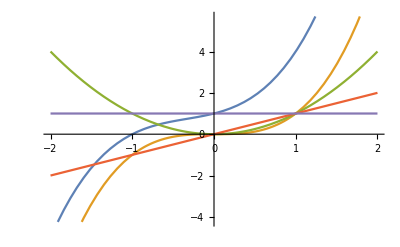

```mathematica
Plot[
{x^3+x^2+x+1,x^3,x^2,x,1}
,{x,-2,2}
]
```

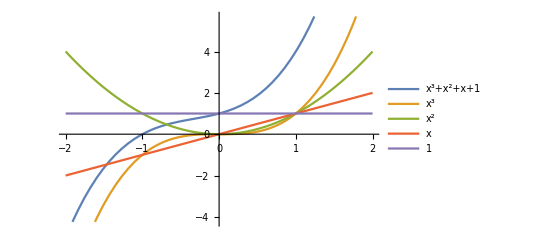

```mathematica
Plot[
{x^3+x^2+x+1,x^3,x^2,x,1}
,{x,-2,2}
,PlotLegends->"Expressions"]
```

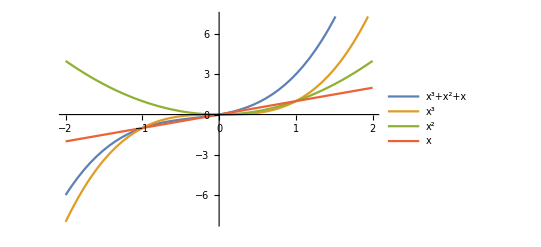

```mathematica
Plot[
{x^3+x^2+x,x^3,x^2,x}
,{x,-2,2}
,PlotLegends->"Expressions"]
```

```mathematica
D[{x^3+x^2+x,x^3,x^2,x},x]
```

{1+2 x+3 x^2,3 x^2,2 x,1}

```mathematica
Normalize@{1,1+2 x+3 x^2}.Normalize@{1,3 x^2}
```

1/(√(1+9 Abs[x]^4) √(1+Abs[1+2 x+3 x^2]^2))+(3 x^2 (1+2 x+3 x^2))/(√(1+9 Abs[x]^4) √(1+Abs[1+2 x+3 x^2]^2))

```mathematica
FullSimplify[Normalize@{1,1+2 x+3 x^2}.Normalize@{1,3 x^2},x∈Reals]
```

(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))

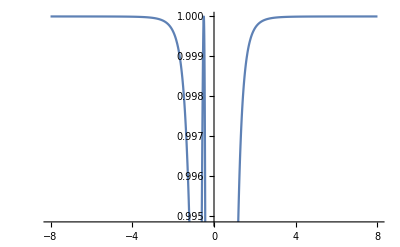

```mathematica
Plot[(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),{x,-8,8}]
```

```mathematica
FullSimplify[Normalize@{1,1+2 x+3 x^2}.Normalize@{1,2x},x∈Reals]
```

(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))

```mathematica
FullSimplify[Normalize@{1,1+2 x+3 x^2}.Normalize@{1,1},x∈Reals]
```

(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))

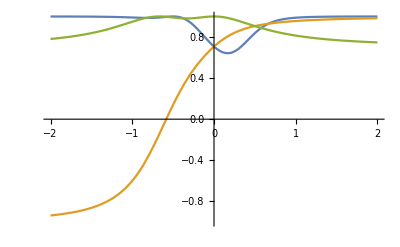

```mathematica
Plot[
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))}
,{x,-2,2}
,PlotRange->{-1,1}
]
```

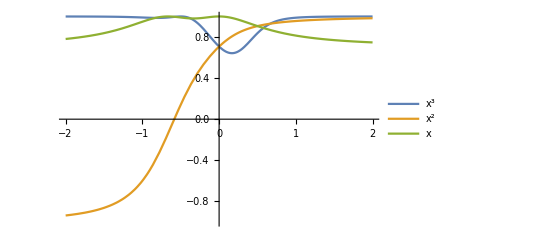

```mathematica
Plot[
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))}
,{x,-2,2}
,PlotRange->{-1,1},PlotLegends->{"x^3","x^2","x"}
]
```

```mathematica
∞/∞
```

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Indeterminate

```mathematica
Limit[∫_-a^a (1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))ⅆx,a->∞]
```

$Aborted

```mathematica
Manipulate[
(∫_-a^a (1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))ⅆx)/a
,{a,0,10000}]
```

```mathematica
MemoryInUse[]
```

294588824

```mathematica
Manipulate[
NIntegrate[(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),{x,-a,a}]/a
,{a,0,10000}]
```

```mathematica
Manipulate[
NIntegrate[(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),{x,-a,a}]/a
,{a,0,10000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.310833}. NIntegrate obtained 1.39472 and 1.01124 for the integral and error estimates.

```mathematica
Manipulate[
NIntegrate[(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),{x,-a,a}]/a
,{a,0,10000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.310833}. NIntegrate obtained 14142.6 and 0.0573919 for the integral and error estimates.

```mathematica
1
```

1

```mathematica
3
```

3

```mathematica
4
```

4

```mathematica
Manipulate[
NIntegrate[(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),{x,-a,a}]/a
,{a,0,100000}]
```

```mathematica
PositiveReals
```

```mathematica
Solve[ϕ==1/(1+ϕ),ϕ,]
```

{{ϕ→1/2 (-1+√5)}}

```mathematica
N[{{ϕ->1/2 (-1+√5)}}]
```

{{ϕ→0.618034}}

```mathematica
FullSimplify[Normalize@{1,1+2 x+3 x^2}.Normalize@{1,0},x∈Reals]
```

1/(√(1+(1+x (2+3 x))^2))

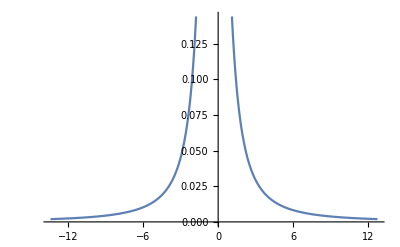

```mathematica
Plot[1/(√(1+(1+x (2+3 x))^2)),{x,-13.437333333333335,12.770666666666667}]
```

```mathematica
Manipulate[
NIntegrate[1/(√(1+(1+x (2+3 x))^2)),{x,-a,a}]/a
,{a,0,100000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-3.10833}. NIntegrate obtained 0.384173 and 0.330204 for the integral and error estimates.

```mathematica
Manipulate[
NIntegrate[1,{x,-a,a}]/a
,{a,0,100000}]
```

```mathematica
∫xⅆx
```

x^2/2

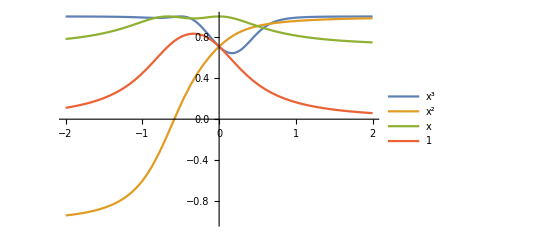

```mathematica
Plot[
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))}
,{x,-2,2}
,PlotRange->{-1,1},PlotLegends->{"x^3","x^2","x","1"}
]
```

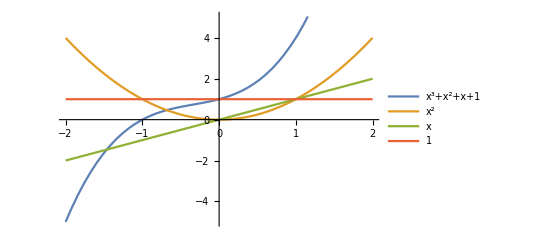

```mathematica
Plot[
{x^3+x^2+x+1,x^2,x,1}
,{x,-2,2}
,PlotLegends->"Expressions"
]
```

```mathematica
Range@10
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Total@{1,2,3,4,5,6,7,8,9,10}
```

55

```mathematica
{1,2,3,4,5,6,7,8,9,10}/55
```

{1/55,2/55,3/55,4/55,1/11,6/55,7/55,8/55,9/55,2/11}

```mathematica
N@{1/55,2/55,3/55,4/55,1/11,6/55,7/55,8/55,9/55,2/11}
```

{0.0181818,0.0363636,0.0545455,0.0727273,0.0909091,0.109091,0.127273,0.145455,0.163636,0.181818}

```mathematica
Total@{1/55,2/55,3/55,4/55,1/11,6/55,7/55,8/55,9/55,2/11}
```

1

```mathematica
Total@{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))}
```

1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))

```mathematica
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))}/(1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))
```

{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),1/(√(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))))}

```mathematica
FullSimplify[
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))}/(1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))
,x∈Reals]
```

{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),1/(√(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))))}

```mathematica
Plot[
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))}
,{x,-2,2}
,PlotRange->{-1,1},PlotLegends->{"x^3","x^2","x","1"}
]
```

-Graphics-

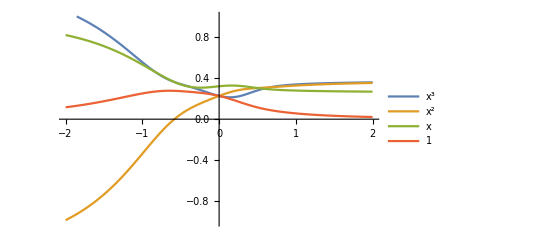

```mathematica
Plot[
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),1/(√(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))))}
,{x,-2,2}
,PlotRange->{-1,1},PlotLegends->{"x^3","x^2","x","1"}
]
```

```mathematica
Total@{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),1/(√(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))))}
```

1/(√(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))))

```mathematica
Simplify[%73]
```

1

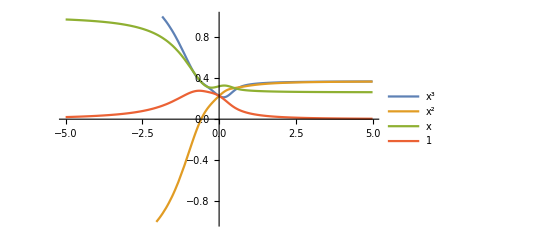

```mathematica
Plot[
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),1/(√(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))))}
,{x,-5,5}
,PlotRange->{-1,1},PlotLegends->{"x^3","x^2","x","1"}
]
```

```mathematica
Abs@{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))}
```

{Abs[(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))],Abs[(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))],Abs[(2+x (2+3 x))/(√(1+(1+x (2+3 x))^2))]/(√2),1/(√Abs[1+(1+x (2+3 x))^2])}

```mathematica
FullSimplify[
Abs@{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),(1+2 x (1+x (2+3 x)))/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))}
,x∈Reals]
```

{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))}

```mathematica
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))}/(Total@{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))})
```

{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),1/(√(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))))}

```mathematica
FullSimplify[
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))}/(Total@{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))})
,x∈Reals]
```

{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),1/(√(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))))}

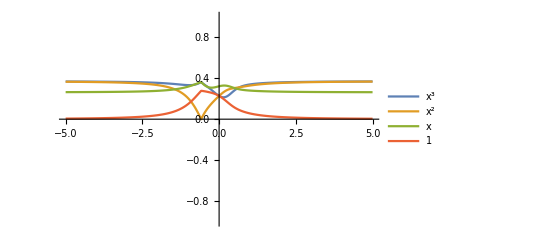

```mathematica
Plot[
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),1/(√(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))))}
,{x,-5,5}
,PlotRange->{-1,1},PlotLegends->{"x^3","x^2","x","1"}
]
```

```mathematica
FullSimplify[
Total@
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),1/(√(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))))}
,x∈Reals]
```

1

```mathematica
FindMinimum[
Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))))
,{x,-.5}]
```

{4.64126×10^-9,{x→-0.584335}}

```mathematica
Solve[Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))))==0,x,Reals]
```

{{x→Root-0.584Root[1+2 #1+4 #1^2+6 #1^3&,1]-0.584335460130277}}

```mathematica
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))}/(Total@{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))})
```

{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),1/(√(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))))}

```mathematica
FullSimplify[{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))}/(Total@{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2)),1/(√(1+(1+x (2+3 x))^2))}),x∈Reals]
```

{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),1/(√(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))))}

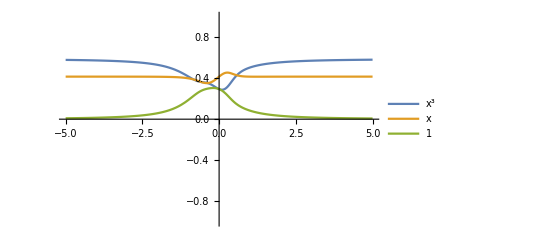

```mathematica
Plot[
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2))))),
1/(√(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))))}
,{x,-5,5}
,PlotRange->{-1,1},PlotLegends->{"x^3","x","1"}
]
```

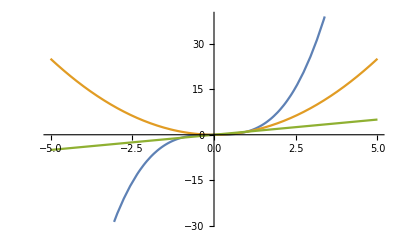

```mathematica
Plot[{x^3,x^2,x},{x,-5,5}]
```

```mathematica
Plot[{x^3,x^2,x},{x,-5,5},ImageSize->Full]
```

-Graphics-

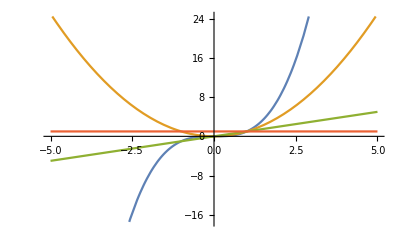

```mathematica
Plot[{x^3,x^2,x,1},{x,-5,5},ImageSize->Full]
```

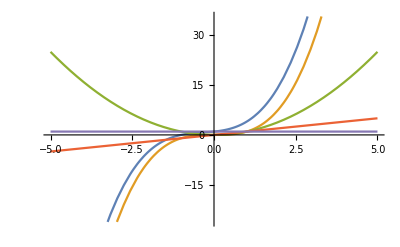

```mathematica
Plot[{x^3+x^2+x+1,x^3,x^2,x,1},{x,-5,5},ImageSize->Full]
```

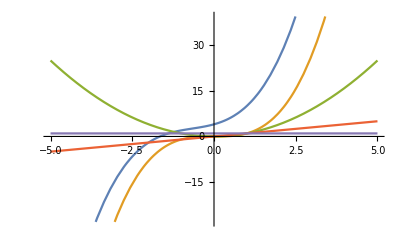

```mathematica
Plot[{x^3+2 x^2+3x+4,x^3,x^2,x,1},{x,-5,5},ImageSize->Full]
```

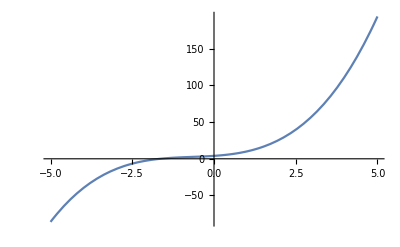

```mathematica
Plot[x^3+2 x^2+3x+4,{x,-5,5},ImageSize->Full]
```

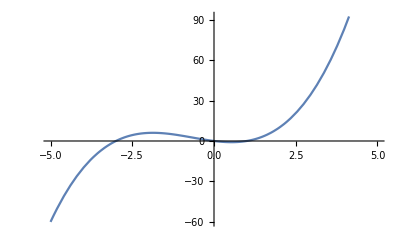

```mathematica
Plot[x^3+2 x^2-3x,{x,-5,5},ImageSize->Full]
```

```mathematica
Plot[
{(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2)) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2))))),1/(√(1+(1+x (2+3 x))^2) (1/(√(1+(1+x (2+3 x))^2))+(2+x (2+3 x))/(√2 √(1+(1+x (2+3 x))^2))+(1+3 x^2 (1+x (2+3 x)))/(√((1+9 x^4) (1+(1+x (2+3 x))^2)))+Abs[1+2 x (1+x (2+3 x))]/(√((1+4 x^2) (1+(1+x (2+3 x))^2)))))}
,{x,-5,5}
,PlotRange->{-1,1},PlotLegends->{"x^3","x^2","x","1"}
]
```

-Graphics-

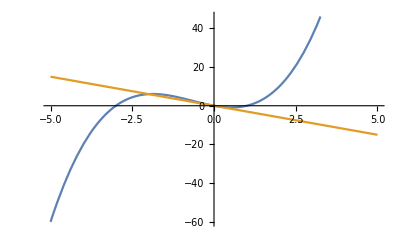

```mathematica
Plot[{x^3+2 x^2-3x,-3x},{x,-5,5},ImageSize->Full]
```

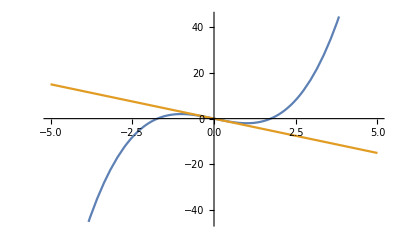

```mathematica
Plot[{x^3-3x,-3x},{x,-5,5},ImageSize->Full]
```

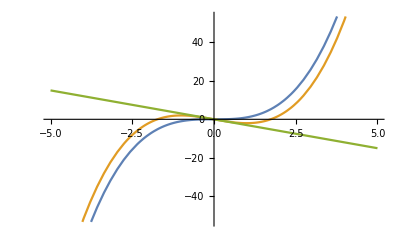

```mathematica
Plot[{x^3,x^3-3x,-3x},{x,-5,5},ImageSize->Full]
```

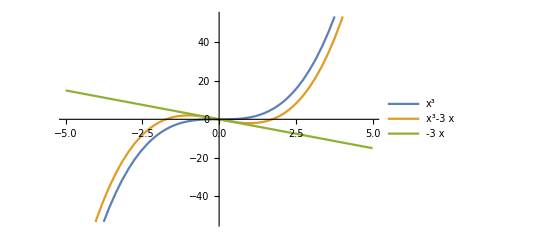

```mathematica
Plot[{x^3,x^3-3x,-3x},{x,-5,5},ImageSize->Full,PlotLegends->"Expressions"]
```

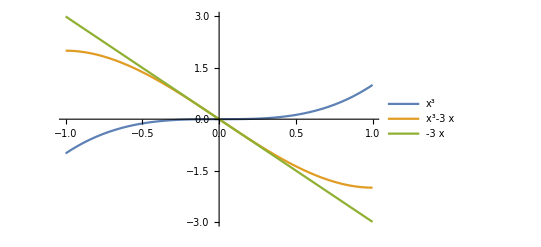

```mathematica
Plot[{x^3,x^3-3x,-3x},{x,-1,1},ImageSize->Full,PlotLegends->"Expressions"]
```

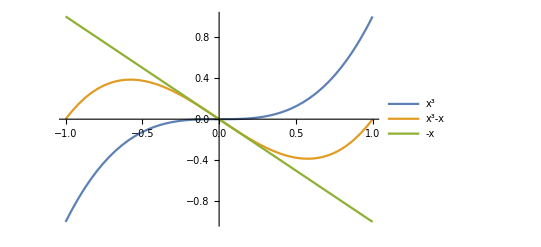

```mathematica
Plot[{x^3,x^3-x,-x},{x,-1,1},ImageSize->Full,PlotLegends->"Expressions"]
```

```mathematica
FullSimplify[Normalize@{x,x^3-x},x∈Reals]
```

{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))}

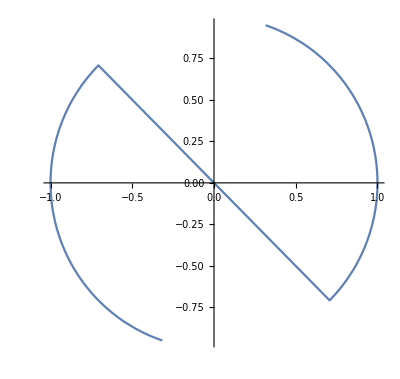

```mathematica
ParametricPlot[
{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))}
,{x,-2,2}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x,x^3-x},
{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))}
},{x,-2,-2+α}]
,{α,0.001,4}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x,x^3-x},
{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))}
},{x,-2,-2+α}
,PlotRange->{{-2,2},{-2,2}}]
,{α,0.001,4}]
```

```mathematica
{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))}/.x->0
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{Indeterminate,Indeterminate}

```mathematica
FullSimplify[Normalize@{x,Sin[x]},x∈Reals]
```

{x/(√(x^2+Sin[x]^2)),Sin[x]/(√(x^2+Sin[x]^2))}

```mathematica
Manipulate[
ParametricPlot[{
{x,Sin[x]},
{x/(√(x^2+Sin[x]^2)),Sin[x]/(√(x^2+Sin[x]^2))}
},{x,-2,-2+α}
,PlotRange->{{-2,2},{-2,2}}]
,{α,0.001,4}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x,Sin[x]},
{x/(√(x^2+Sin[x]^2)),Sin[x]/(√(x^2+Sin[x]^2))}
},{x,-2π,-2π+α}]
,{α,0.001,4π}]
```

```mathematica
FullSimplify[Normalize@{x,Sinc[x]},x∈Reals]
```

{x/(√(x^2+Sinc[x]^2)),Sinc[x]/(√(x^2+Sinc[x]^2))}

```mathematica
Manipulate[
ParametricPlot[{
{x,Sinc[x]},
{x/(√(x^2+Sinc[x]^2)),Sinc[x]/(√(x^2+Sinc[x]^2))}
},{x,-2π,-2π+α}]
,{α,0.001,4π}]
```

```mathematica
FullSimplify[Normalize@{x^2,x(x x- 1)},x∈Reals]
```

{Abs[x]/(√(1-x^2+x^4)),(x (-1+x^2))/(√(x^2-x^4+x^6))}

```mathematica
Manipulate[
ParametricPlot[{
{x^2,x(x x- 1)},
{Abs[x]/(√(1-x^2+x^4)),(x (-1+x^2))/(√(x^2-x^4+x^6))}
},{x,-2π,-2π+α}]
,{α,0.001,4π}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x,x^3-x},
{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))}
},{x,-2,-2+α}
,PlotRange->{{-2,2},{-2,2}}]
,{α,0.001,4}]
```

```mathematica
{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))}-{x,x^3-x}
```

{-x+x/(√(x^2+(x-x^3)^2)),x-x^3+(x (-1+x^2))/(√(x^2+(x-x^3)^2))}

```mathematica
FullSimplify[{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))}-{x,x^3-x},x∈Reals]
```

{x (-1+1/(√(x^2 (2-2 x^2+x^4)))),x-x^3+(x (-1+x^2))/(√(x^2+(x-x^3)^2))}

```mathematica
Manipulate[
ParametricPlot[{
{x,x^3-x},
{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))},
{x a (-1+1/(√(a^2 (2-2 a^2+a^4)))),x (a-a^3+(a (-1+a^2))/(√(a^2+(a-a^3)^2)))}
},{x,-2,-2+α}
,PlotRange->{{-2,2},{-2,2}}]
,{α,0.001,4}]
```

```mathematica
{x (-1+1/(√(x^2 (2-2 x^2+x^4)))),x-x^3+(x (-1+x^2))/(√(x^2+(x-x^3)^2))}/.x->a
```

{a (-1+1/(√(a^2 (2-2 a^2+a^4)))),a-a^3+(a (-1+a^2))/(√(a^2+(a-a^3)^2))}

```mathematica
Manipulate[
ParametricPlot[{
{x,x^3-x},
{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))},
{x,x (a-a^3+(a (-1+a^2))/(√(a^2+(a-a^3)^2)))}
},{x,-2,-2+α}
,PlotRange->{{-2,2},{-2,2}}]
,{α,0.001,4}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x,x^3-x},
{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))},
{x a (-1+1/(√(a^2 (2-2 a^2+a^4)))),x (a-a^3+(a (-1+a^2))/(√(a^2+(a-a^3)^2)))}
},{x,-2,-2+α}
,PlotRange->{{-2,2},{-2,2}}]
,{α,0.001,4}]
```

```mathematica
D[{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))},x]
```

{-(x (2 x+2 (1-3 x^2) (x-x^3)))/(2 (x^2+(x-x^3)^2)^(3/2))+1/(√(x^2+(x-x^3)^2)),-(x (-1+x^2) (2 x+2 (1-3 x^2) (x-x^3)))/(2 (x^2+(x-x^3)^2)^(3/2))+(2 x^2)/(√(x^2+(x-x^3)^2))+(-1+x^2)/(√(x^2+(x-x^3)^2))}

```mathematica
FullSimplify[D[{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))},x],x∈Reals]
```

{-(2 (-1+x^2) Abs[x])/((2-2 x^2+x^4)^(3/2)),(2 Abs[x])/((2-2 x^2+x^4)^(3/2))}

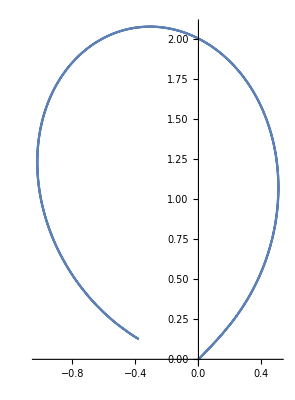

```mathematica
ParametricPlot[
{-(2 (-1+x^2) Abs[x])/((2-2 x^2+x^4)^(3/2)),(2 Abs[x])/((2-2 x^2+x^4)^(3/2))}
,{x,-2,2}]
```

```mathematica
FullSimplify[Norm@D[{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))},x],x∈Reals]
```

(2 Abs[x])/(2-2 x^2+x^4)

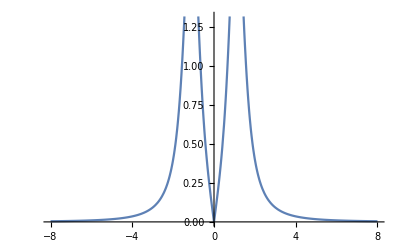

```mathematica
Plot[(2 Abs[x])/(2-2 x^2+x^4),{x,-8,8}]
```

```mathematica
Plot[(2 Abs[x])/(2-2 x^2+x^4),{x,-8,8}]
```

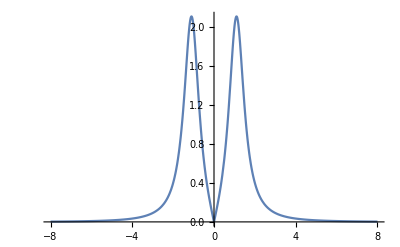

```mathematica
Plot[(2 Abs[x])/(2-2 x^2+x^4),{x,-8,8},PlotRange->Full]
```

```mathematica
FullSimplify[D[(2 Abs[x])/(2-2 x^2+x^4),x],x∈Reals]
```

((4 x-6 x^3) Abs[x]+4 Sign[x])/((2-2 x^2+x^4)^2)

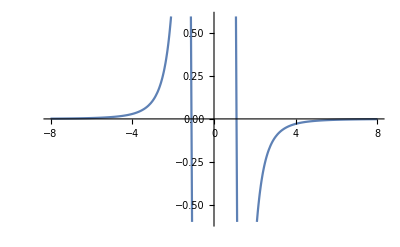

```mathematica
Plot[((4 x-6 x^3) Abs[x]+4 Sign[x])/((2-2 x^2+x^4)^2),{x,-8,8}]
```

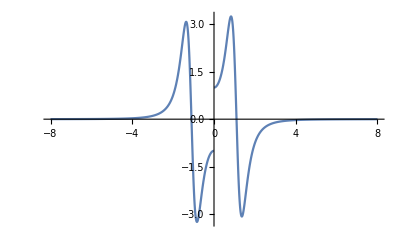

```mathematica
Plot[((4 x-6 x^3) Abs[x]+4 Sign[x])/((2-2 x^2+x^4)^2),{x,-8,8},PlotRange->Full]
```

```mathematica
Manipulate[
ParametricPlot[
FullSimplify[Normalize@{x,x^3-x}.Normalize@{x,a},Element[x,Reals]]
,{x,-4,4}]
,{a,-4,4}]
```

```mathematica
Factor[x^4-x^3]
```

(-1+x) x^3

```mathematica
Manipulate[
ParametricPlot[{
{x,x^3-x},
{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))}
},{x,-2,-2+α}
,PlotRange->{{-2,2},{-2,2}}]
,{α,0.001,4}]
```

```mathematica
FullSimplify[Normalize@{x,x},x∈Reals]
```

{Sign[x]/(√2),Sign[x]/(√2)}

```mathematica
Manipulate[
ParametricPlot[{
{x,x},
{Sign[x]/(√2),Sign[x]/(√2)}
},{x,-2,-2+α}
,PlotRange->{{-2,2},{-2,2}}]
,{α,0.001,4}]
```

```mathematica
FullSimplify[Normalize@{x,x^2},x∈Reals]
```

{x/(√(x^2+x^4)),Abs[x]/(√(1+x^2))}

```mathematica
Manipulate[
ParametricPlot[{
{x,x^2},
{x/(√(x^2+x^4)),Abs[x]/(√(1+x^2))}
},{x,-2,-2+α}
,PlotRange->{{-2,2},{-2,2}}]
,{α,0.001,4}]
```

```mathematica
FullSimplify[Normalize@{x,x^3},x∈Reals]
```

{x/(√(x^2+x^6)),(x Abs[x])/(√(1+x^4))}

```mathematica
Manipulate[
ParametricPlot[{
{x,x^3},
{x/(√(x^2+x^6)),(x Abs[x])/(√(1+x^4))}
},{x,-2,-2+α}
,PlotRange->{{-2,2},{-2,2}}]
,{α,0.001,4}]
```

```mathematica
FullSimplify[Normalize@{x,x^4},x∈Reals]
```

```mathematica
Manipulate[
ParametricPlot[{
{x,x^4},
{x/(√(x^2+x^8)),x^4/(√(x^2+x^8))}
},{x,-2,-2+α}
,PlotRange->{{-2,2},{-2,2}}]
,{α,0.001,4}]
```

```mathematica
FullSimplify[Normalize@{x,x^6},x∈Reals]
```

{x/(√(x^2+x^12)),x^6/(√(x^2+x^12))}

```mathematica
Manipulate[
ParametricPlot[{
{x,x^6},
{x/(√(x^2+x^12)),x^6/(√(x^2+x^12))}
},{x,-2,-2+α}
,PlotRange->{{-2,2},{-2,2}}]
,{α,0.001,4}]
```

```mathematica
ComplexPlot[(z^2+1)/(z^2-1),{z,-2-2I,2+2I}]
```

-Graphics-

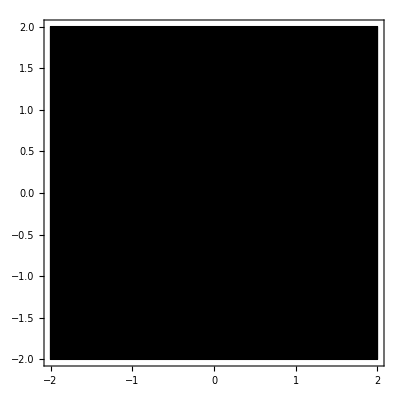

```mathematica
ComplexPlot[(z^2+1)/(z^2-1),{z,-2-2I,2+2I},PlotLegends->Automatic]
```

```mathematica
ComplexPlot[(z^2+1)/(z^2-1),{z,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
ComplexPlot[z^2,{z,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
ComplexPlot[Exp[z],{z,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
ComplexPlot[z,{z,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
Manipulate[
ComplexPlot[(1-a)z+a z^2,{z,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
,{a,0,1}]
```

```mathematica
Manipulate[
ComplexPlot[
(1-a)z+a Exp[z]
,{z,-2-2I,2+2I}
,ColorFunction->"CyclicLogAbsArg"]
,{a,0,1}]
```

```mathematica
Manipulate[
ComplexPlot[
(1-a)z+a ((z^2+1)/(z^2-1))
,{z,-2-2I,2+2I}
,ColorFunction->"CyclicLogAbsArg"]
,{a,0,1}]
```

```mathematica
PDF[NormalDistribution[],t]
```

(ⅇ^(-t^2/2))/(√(2 π))

```mathematica
ⅇ^(-t^2/2)RotationMatrix[θ]
```

{{ⅇ^(-t^2/2) Cos[θ],-ⅇ^(-t^2/2) Sin[θ]},{ⅇ^(-t^2/2) Sin[θ],ⅇ^(-t^2/2) Cos[θ]}}

```mathematica
ⅇ^(-t^2/2)RotationMatrix[π/2]
```

{{0,-ⅇ^(-t^2/2)},{ⅇ^(-t^2/2),0}}

```mathematica
{t,t}.{{0,-ⅇ^(-t^2/2)},{ⅇ^(-t^2/2),0}}
```

{ⅇ^(-t^2/2) t,-ⅇ^(-t^2/2) t}

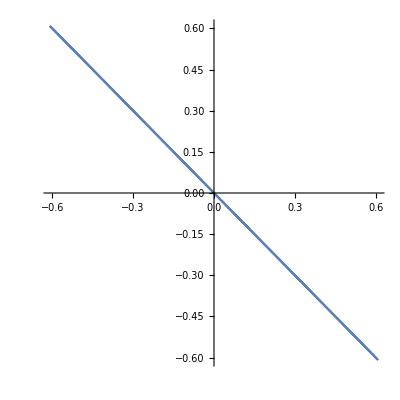

```mathematica
ParametricPlot[
{ⅇ^(-t^2/2) t,-ⅇ^(-t^2/2) t}
,{t,-2π,2π}
]
```

```mathematica
t-t ⅇ^(-t^2/2)
```

t-ⅇ^(-t^2/2) t

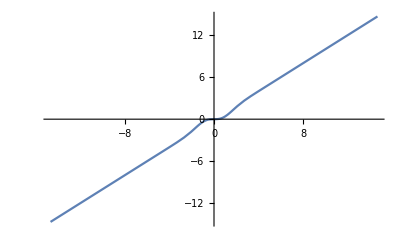

```mathematica
Plot[t-ⅇ^(-t^2/2) t,{t,-14.696938456699069,14.696938456699069}]
```

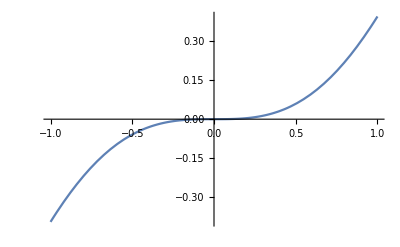

```mathematica
Plot[t-ⅇ^(-t^2/2) t,{t,-1,1}]
```

```mathematica
1-ⅇ^(-t^2/2)
```

1-ⅇ^(-t^2/2)

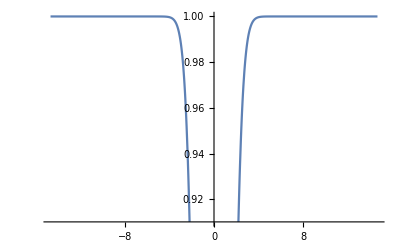

```mathematica
Plot[1-ⅇ^(-t^2/2),{t,-14.696938456699069,14.696938456699069}]
```

```mathematica
1-ⅇ^(-t^2/2)
```

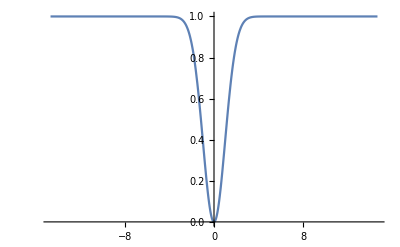

```mathematica
Plot[1-ⅇ^(-t^2/2),{t,-14.696938456699069,14.696938456699069},PlotRange->Full]
```

```mathematica
Integrate[1-ⅇ^(-t^2/2),t]
```

t-√(π/2) Erf[t/(√2)]

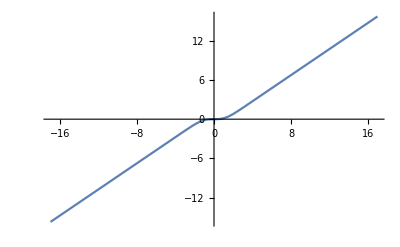

```mathematica
Plot[t-√(π/2) Erf[t/(√2)],{t,-16.970562748477143,16.970562748477143}]
```

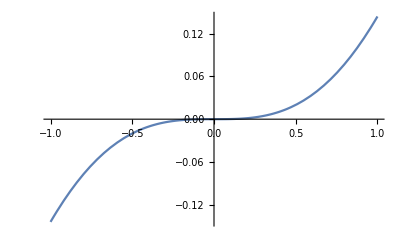

```mathematica
Plot[t-√(π/2) Erf[t/(√2)],{t,-1,1}]
```

```mathematica
t+(ⅇ^(-t^2/2))-t
```

ⅇ^(-t^2/2)

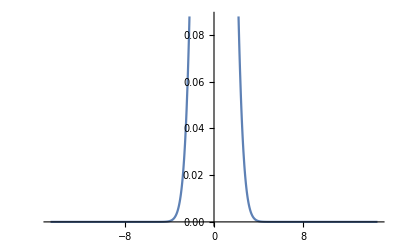

```mathematica
Plot[ⅇ^(-t^2/2),{t,-14.696938456699069,14.696938456699069}]
```

```mathematica
t+(ⅇ^(-t^2/2))(-t)
```

t-ⅇ^(-t^2/2) t

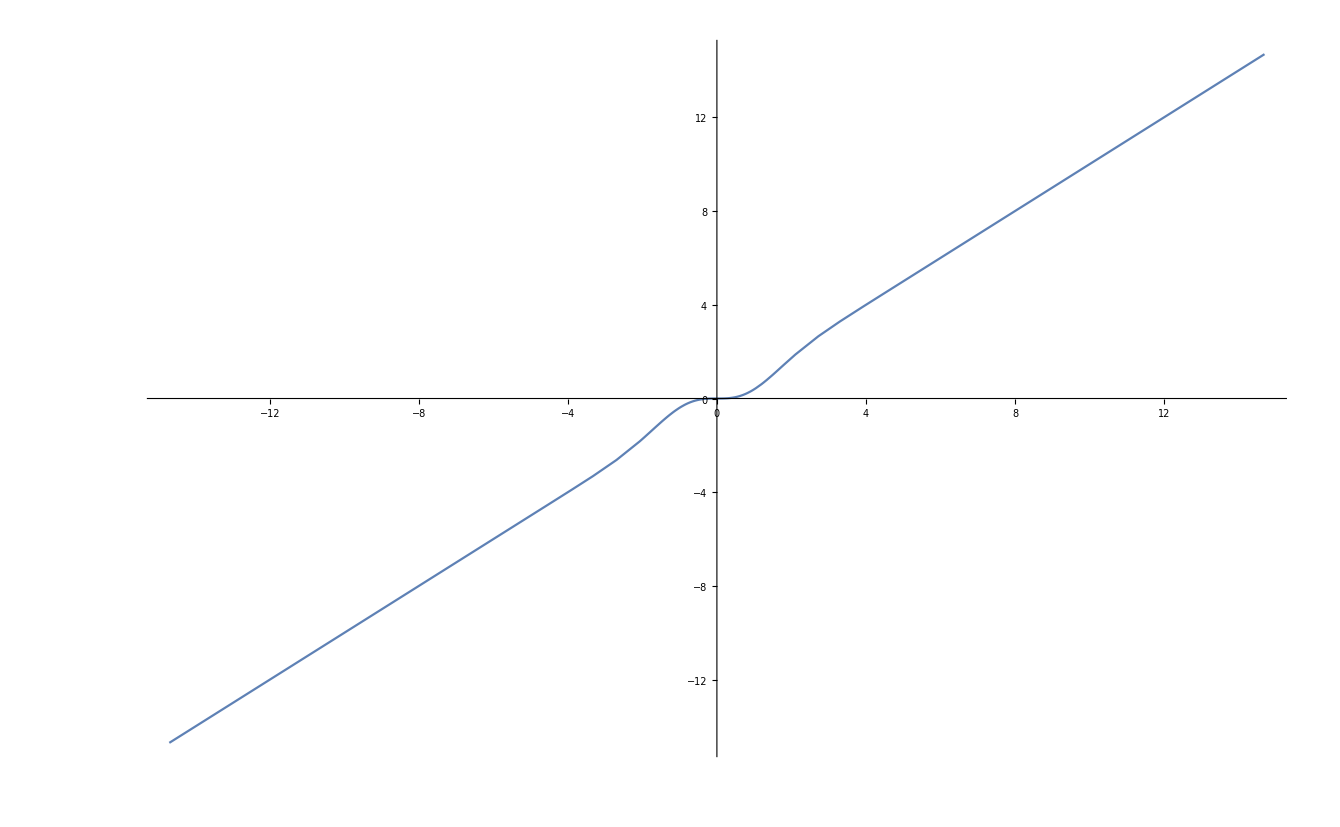

```mathematica
Plot[t-ⅇ^(-t^2/2) t,{t,-14.696938456699069,14.696938456699069}]
```

```mathematica
ⅇ^(-t^2/2)
```

ⅇ^(-t^2/2)

```mathematica
Plot[ⅇ^(-t^2/2),{t,-14.696938456699069,14.696938456699069}]
```

-Graphics-

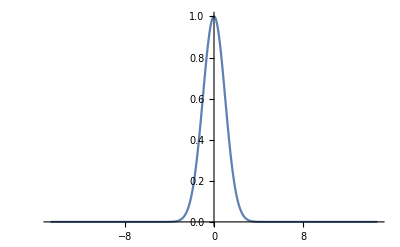

```mathematica
Plot[ⅇ^(-t^2/2),{t,-14.696938456699069,14.696938456699069},PlotRange->Full]
```

```mathematica
Integrate[1-ⅇ^(-t^2/2),t]
```

t-√(π/2) Erf[t/(√2)]

```mathematica
Plot[t-√(π/2) Erf[t/(√2)],{t,-16.970562748477143,16.970562748477143}]
```

-Graphics-

```mathematica
(1-ⅇ^(-t^2/2))t+(ⅇ^(-t^2/2))t
```

ⅇ^(-t^2/2) t+(1-ⅇ^(-t^2/2)) t

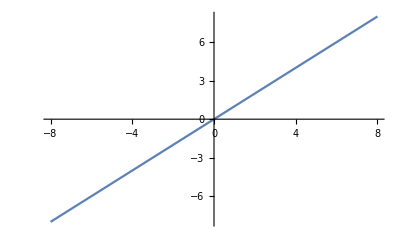

```mathematica
Plot[ⅇ^(-t^2/2) t+(1-ⅇ^(-t^2/2)) t,{t,-8,8}]
```

```mathematica
(1-ⅇ^(-t^2/2))t+(ⅇ^(-t^2/2))(-t)
```

-ⅇ^(-t^2/2) t+(1-ⅇ^(-t^2/2)) t

```mathematica
Simplify[-ⅇ^(-t^2/2) t+(1-ⅇ^(-t^2/2)) t]
```

t-2 ⅇ^(-t^2/2) t

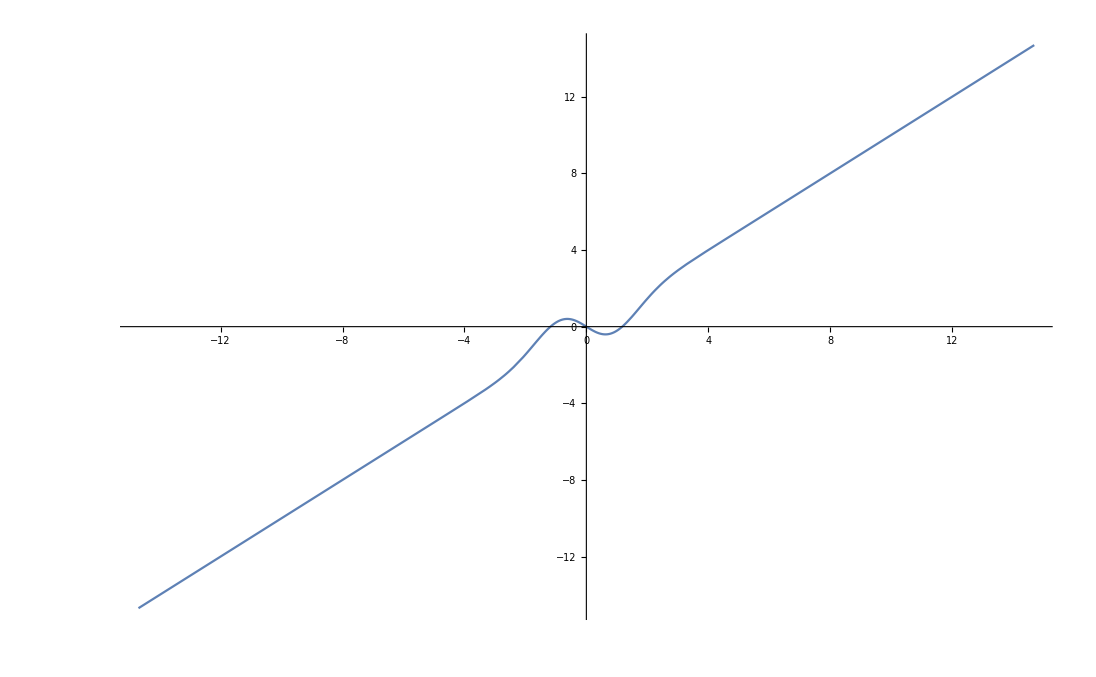

```mathematica
Plot[t-2 ⅇ^(-t^2/2) t,{t,-14.696938456699069,14.696938456699069}]
```

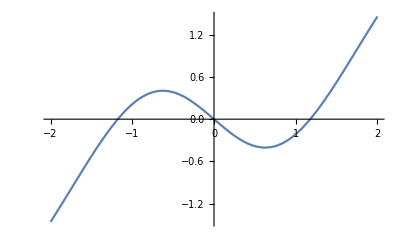

```mathematica
Plot[t-2 ⅇ^(-t^2/2) t,{t,-2,2}]
```

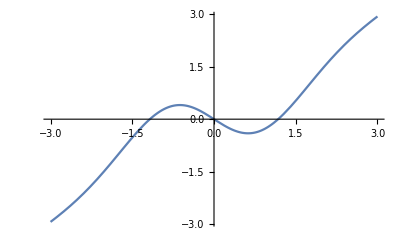

```mathematica
Plot[t-2 ⅇ^(-t^2/2) t,{t,-3,3}]
```

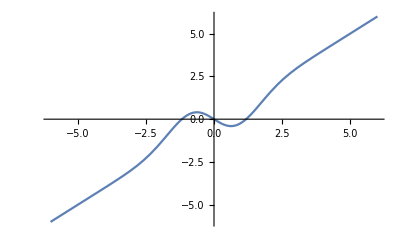

```mathematica
Plot[t-2 ⅇ^(-t^2/2) t,{t,-6,6}]
```

```mathematica
(1-a)t+a (t-2 ⅇ^(-t^2/2) t)
```

(1-a) t+a (t-2 ⅇ^(-t^2/2) t)

```mathematica
Simplify[(1-a) t+a (t-2 ⅇ^(-t^2/2) t)]
```

t-2 a ⅇ^(-t^2/2) t

```mathematica
Manipulate[Plot[t-2 a ⅇ^(-t^2/2) t,{t,-1.4334000879288848,1.4334000879288848}],{a,-3.,3.}]
```

```mathematica
Manipulate[Plot[t-2 a ⅇ^(-t^2/2) t,{t,-6,6}],{a,0,1}]
```

```mathematica
{t,t}.RotationMatrix[π]
```

{-t,-t}

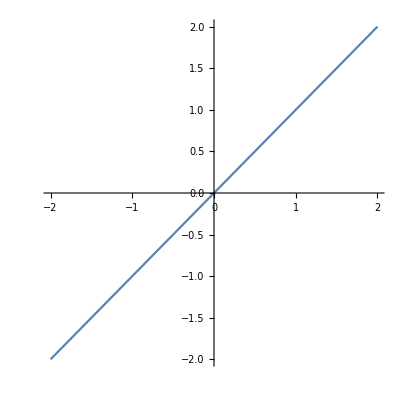

```mathematica
ParametricPlot[{-t,-t},{t,-2,2}]
```

```mathematica
{t,t}.RotationMatrix[π/2]
```

{t,-t}

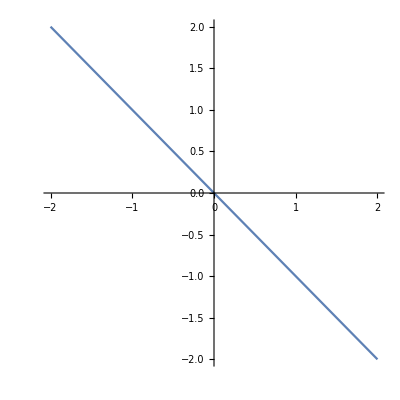

```mathematica
ParametricPlot[{t,-t},{t,-2,2}]
```

```mathematica
{t,t}.RotationMatrix[Sin[t] π/2]
```

{t Cos[1/2 π Sin[t]]+t Sin[1/2 π Sin[t]],t Cos[1/2 π Sin[t]]-t Sin[1/2 π Sin[t]]}

```mathematica
(1+Cos[π t])/2
```

1/2 (1+Cos[π t])

```mathematica
{t,t}.RotationMatrix[(1+Cos[π t])/2 π/2]
```

{t Cos[1/4 π (1+Cos[π t])]+t Sin[1/4 π (1+Cos[π t])],t Cos[1/4 π (1+Cos[π t])]-t Sin[1/4 π (1+Cos[π t])]}

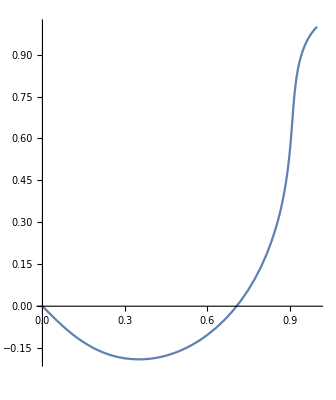

```mathematica
ParametricPlot[
{t Cos[1/4 π (1+Cos[π t])]+t Sin[1/4 π (1+Cos[π t])],t Cos[1/4 π (1+Cos[π t])]-t Sin[1/4 π (1+Cos[π t])]}
,{t,0,1}]
```

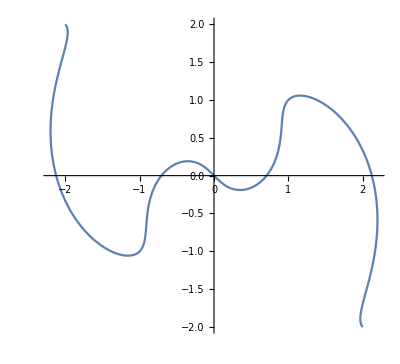

```mathematica
ParametricPlot[
{t Cos[1/4 π (1+Cos[π t])]+t Sin[1/4 π (1+Cos[π t])],t Cos[1/4 π (1+Cos[π t])]-t Sin[1/4 π (1+Cos[π t])]}
,{t,-2,2}]
```

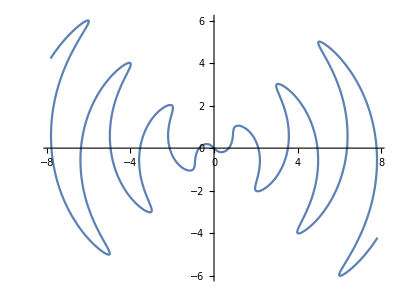

```mathematica
ParametricPlot[
{t Cos[1/4 π (1+Cos[π t])]+t Sin[1/4 π (1+Cos[π t])],t Cos[1/4 π (1+Cos[π t])]-t Sin[1/4 π (1+Cos[π t])]}
,{t,-2π,2π}]
```

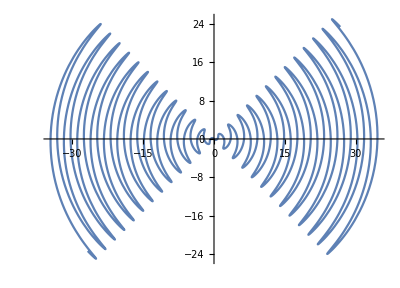

```mathematica
ParametricPlot[
{t Cos[1/4 π (1+Cos[π t])]+t Sin[1/4 π (1+Cos[π t])],t Cos[1/4 π (1+Cos[π t])]-t Sin[1/4 π (1+Cos[π t])]}
,{t,-8π,8π}]
```

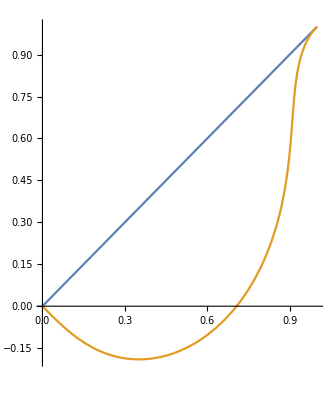

```mathematica
ParametricPlot[{
{t,t},
{t Cos[1/4 π (1+Cos[π t])]+t Sin[1/4 π (1+Cos[π t])],t Cos[1/4 π (1+Cos[π t])]-t Sin[1/4 π (1+Cos[π t])]}
},{t,0,1}]
```

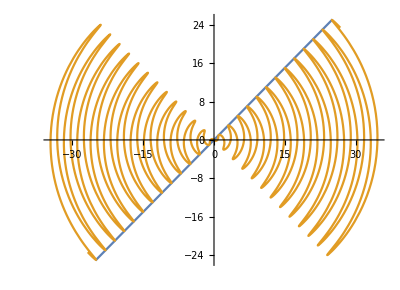

```mathematica
ParametricPlot[{
{t,t},
{t Cos[1/4 π (1+Cos[π t])]+t Sin[1/4 π (1+Cos[π t])],t Cos[1/4 π (1+Cos[π t])]-t Sin[1/4 π (1+Cos[π t])]}
},{t,-8π,8π}]
```

```mathematica
{t,t}.RotationMatrix[Exp[-t^2/2] π/2]
```

{t Cos[1/2 ⅇ^(-t^2/2) π]+t Sin[1/2 ⅇ^(-t^2/2) π],t Cos[1/2 ⅇ^(-t^2/2) π]-t Sin[1/2 ⅇ^(-t^2/2) π]}

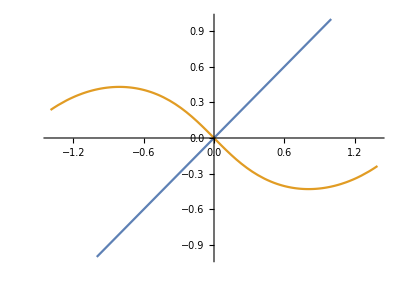

```mathematica
ParametricPlot[{
{t,t},
{t Cos[1/2 ⅇ^(-t^2/2) π]+t Sin[1/2 ⅇ^(-t^2/2) π],t Cos[1/2 ⅇ^(-t^2/2) π]-t Sin[1/2 ⅇ^(-t^2/2) π]}
},{t,-1,1}]
```

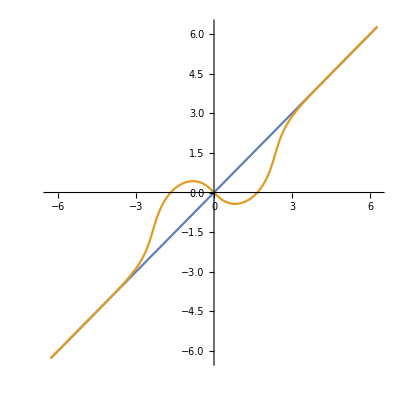

```mathematica
ParametricPlot[{
{t,t},
{t Cos[1/2 ⅇ^(-t^2/2) π]+t Sin[1/2 ⅇ^(-t^2/2) π],t Cos[1/2 ⅇ^(-t^2/2) π]-t Sin[1/2 ⅇ^(-t^2/2) π]}
},{t,-2π,2π}]
```

```mathematica
Plot[t-2 ⅇ^(-t^2/2) t,{t,-6,6}]
```

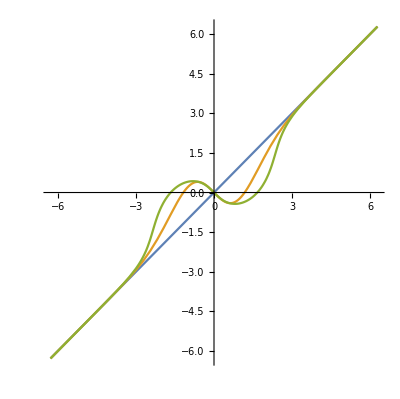

```mathematica
ParametricPlot[{
{t,t},
{t,t-2 ⅇ^(-t^2/2) t},
{t Cos[1/2 ⅇ^(-t^2/2) π]+t Sin[1/2 ⅇ^(-t^2/2) π],t Cos[1/2 ⅇ^(-t^2/2) π]-t Sin[1/2 ⅇ^(-t^2/2) π]}
},{t,-2π,2π}]
```

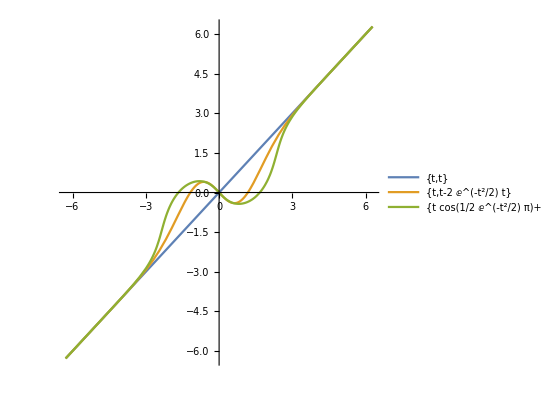

```mathematica
ParametricPlot[{
{t,t},
{t,t-2 ⅇ^(-t^2/2) t},
{t Cos[1/2 ⅇ^(-t^2/2) π]+t Sin[1/2 ⅇ^(-t^2/2) π],t Cos[1/2 ⅇ^(-t^2/2) π]-t Sin[1/2 ⅇ^(-t^2/2) π]}
},{t,-2π,2π}
,PlotLegends->"Expressions"]
```

```mathematica
ComplexPlot[Gamma[z],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics-

```mathematica
ComplexPlot[z^3-z,{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics-

```mathematica
ComplexPlot[Zeta[z],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics-

```mathematica
ComplexPlot[
Zeta[z]
,{z,-2-2I,2+2I}
,ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

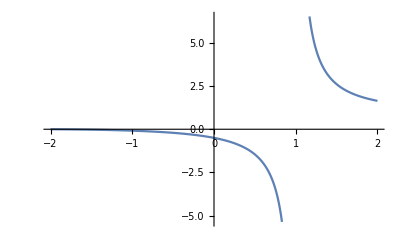

```mathematica
Plot[Zeta[x],{x,-2,2}]
```

```mathematica
Solve[Zeta[x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-56}}

```mathematica
Solve[Zeta[x]==0,x,Reals]
```

{{x→ConditionalExpression[-2 C[1],C[1]∈ℤ&&C[1]≥1]}}

```mathematica
Zeta[-1]
```

-1/12